```mathematica
Clear["Global`*"] (* This command clears everything *)
```

```mathematica
(* Define Pauli matrices and σ+, σ- operators in matrix form *)
sx={{0,1},{1,0}};
sy={{0,-ⅈ},{ⅈ,0}};
sz={{1,0},{0,-1}};
sp=(sx+ⅈ sy)/2;
sm=(sx-ⅈ sy)/2;
```

```mathematica
(* Define inner and outer products suitable for quantum states *)
out[a_,b_]:=Outer[Times,a,Conjugate[b]] (* This gives |a><b| *)
in[a_,b_]:=Inner[Times,Conjugate[a],b,Plus] (* The in[a_,b_] function is equivalent to Conjugate[a].b and gives <a|b> *)
```

```mathematica
initialstate={0,1}; (* initial state here is |g>, i.e. the two-level ground state *)
```

```mathematica
(* Define the effective Hamiltonian for the no-jump evolution *)
Heff[Ω_,Γ_]=Ω/2 sx-ⅈ Γ/2 sp.sm;
```

```mathematica
(* Without jumps, the state evolves from the initial state according to the following, where n is the number of steps *)
statensteps[Ω_,Γ_,tstep_,n_]:=MatrixPower[(IdentityMatrix[2]-ⅈ Heff[Ω,Γ]tstep),n].initialstate
```

```mathematica
(* Normalise *)
```

```mathematica
dp[Ω_,Γ_,tstep_,n_]:=1-in[statensteps[Ω,Γ,tstep,n],statensteps[Ω,Γ,tstep,n]]
```

```mathematica
statenormnsteps[Ω_,Γ_,tstep_,n_]:=statensteps[Ω,Γ,tstep,n]/(√(1-dp[Ω,Γ,tstep,n]))
```

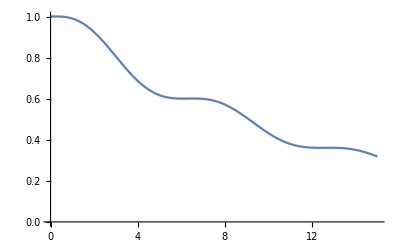

```mathematica
(* Check overlap of unnormalised state *)
ListPlot[Table[{0.01n,in[statensteps[1,1/6,0.01,n],statensteps[1,1/6,0.01,n]]},{n,0,15/0.01}],Joined->True]
```

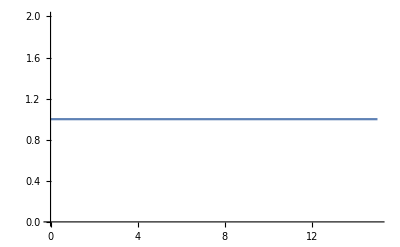

```mathematica
(* Check normalisation of normalised state *)
ListPlot[Table[{0.01n,in[statenormnsteps[1,1/6,0.01,n],statenormnsteps[1,1/6,0.01,n]]},{n,0,15/0.01}],Joined->True]
```

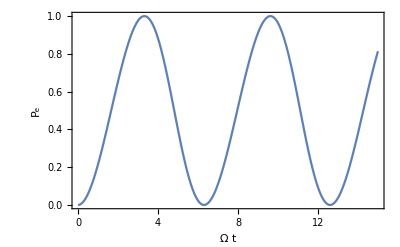

```mathematica
(* Excited state population *)
ListPlot[Table[{0.01n,in[statenormnsteps[1,1/6,0.01,n],sp.sm.statenormnsteps[1,1/6,0.01,n]]},{n,0,15/0.01}],Joined->True,Frame->True,PlotRange->{0,1},FrameLabel->{"Ω t","P_e"}]
```